Asignación de nombres a cosas

Con frecuencia, en Wolfram Language conviene usar % para referirse al resultado más reciente que se haya obtenido, principalmente cuando se está en una etapa inicial de la resolución de algún problema.

Efectúe un cómputo sencillo:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

% presenta el resultado del último cómputo:

```mathematica
%
```

{1,2,3,4,5,6,7,8,9,10}

Esto eleva al cuadrado el resultado más reciente:

```mathematica
%^2
```

{1,4,9,16,25,36,49,64,81,100}

Si posteriormente se va a hacer referencia a un resultado, se le puede asignar un nombre. Por ejemplo, puede escribirse thing=Range[10] para asignar thing como nombre del resultado de Range[10].

Asigne thing como nombre del resultado de Range[10]:

```mathematica
thing=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Cada vez que surja la palabra thing, se sustituirá por el resultado de Range[10]:

```mathematica
thing
```

{1,2,3,4,5,6,7,8,9,10}

Eleve al cuadrado el valor de thing:

```mathematica
thing^2
```

{1,4,9,16,25,36,49,64,81,100}

Puede asignarse un nombre al resultado de un cómputo aún cuando no se muestre el resultado. Para evitar que se vea el resultado, se termina la entrada con ; (punto y coma).

Asigne un nombre a la lista de un millón de elementos, .08pero sin mostrar la lista:

```mathematica
millionlist=Range[1000000];
```

Encuentre el total de todos los elementos de la lista:

```mathematica
Total[millionlist]
```

500000500000

Al asignar un nombre a alguna cosa, dicho nombre sigue vigente hasta que se borre explícitamente.

Asigne x al valor 42:

```mathematica
x=42
```

42

En lo que sigue, podría pensarse que el resultado sería {x,y,z}, pero x tiene el valor 42:

```mathematica
{x,y,z}
```

{42,y,z}

Para borrar una asignación se usa Clear.

Borre cualquier asignación que se haya hecho a x:

```mathematica
Clear[x]
```

Así, x no se sustituye, tal como sucede con y y z:

```mathematica
{x,y,z}
```

{x,y,z}

El asignar un valor global a x, tal como x=42, es algo potencialmente importante, ya que puede afectar a todo lo que uno haga en una sesión (al menos, hasta que se borre x). Es mucho más seguro, y de gran utilidad, asignar a x un valor temporal que sea local, dentro de un módulo.

Lo siguiente asigna a x el valor Range[10] dentro de Module:

```mathematica
Module[{x=Range[10]},x^2]
```

{1,4,9,16,25,36,49,64,81,100}

x no tiene asignado ningún valor fuera del módulo:

```mathematica
x
```

x

Dentro de un módulo se pueden tener tantas variables locales como se desee.

Defina las variables locales x y n, y calcular x^n usando los valores que se les haya asignado:

```mathematica
Module[{x=Range[10],n=2},x^n]
```

{1,4,9,16,25,36,49,64,81,100}

En el estilo de programación funcional usado hasta ahora en casi todo el libro, se realizan secuencias de operaciones mediante la aplicación de secuencias de funciones. Este estilo de programación es muy directo y poderoso, y además excepcionalmente adecuado para Wolfram Language.

Una vez que se ha visto como definir variables, puede usarse un estilo diferente, donde no se pasan los resultados directamente de una función a otra, sino que se asignan como valores de variables a ser usadas posteriormente. Este tipo de programación se denomina programación procedimental, y se ha usado en lenguajes de bajo nivel desde las épocas tempranas de la computación.

A veces esto tiene cierta utilidad en Wolfram Language, aunque ha sido eclipsada por la programación funcional, de uno u otro modo, así como por la programación basada en patrones, que se verá posteriormente.

Para especificar secuencias de acciones en Wolfram Language simplemente se separan con un punto y coma (;). (El poner un punto y coma al final es equivalente a especificar una acción vacía, lo que tiene por efecto que el resultado no se muestre en la pantalla).

Realice una secuencia de operaciones; el resultado es lo producido .08por la última operación:

```mathematica
x=Range[10];y=x^2;y=y+10000
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

En el ejemplo anterior se definieron valores globales para x e y; no hay que olvidarse de borrarlas:

```mathematica
Clear[x,y]
```

Dentro de Module se pueden usar signos de punto y coma para realizar secuencias de operaciones.

Lo siguiente realiza una secuencia de operaciones, mientras se mantiene a x y y como variables locales:

```mathematica
Module[{x,y},x=Range[10];y=x^2;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

Pueden mezclarse variables locales que tengan valores iniciales con otras que no los tengan:

```mathematica
Module[{x,y,n=2},x=Range[10];y=x^n;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

Se pueden anidar módulos; esto es muy útil cuando se elaboran programas muy grandes en los que se quiere trabajar aislando diferentes secciones del código.

Vocabulario

% |   | el resultado más reciente que se haya obtenido
x=valor |   | asigna un valor
Clear[x] |   | borra un valor
Module[{x=valor}, ...] |   | establece una variable temporal 
expr; |   | realiza una labor de cómputo, sin mostrar el resultado al final
expr_1;  expr_2;  ... |   | efectúa una secuencia de procesos de cómputo

"7 Exercises Available" | "Get Started »"

Use Module para calcular x^2+x donde x es Range[10]. »

| Expected output: |  
  | {2,6,12,20,30,42,56,72,90,110} |

Use Module para generar una lista de 10 enteros aleatorios hasta el 100, y cree una columna con la lista original más los resultados de aplicarle Sort, Max y Total. »

| Sample expected output: |  
  | {38,25,79,92,19,68,53,39,71,2}
{2,19,25,38,39,53,68,71,79,92}
92
486 |

Use Module para generar un collage de imágenes con la foto de una jirafa, más los resultados de aplicarle Blur, EdgeDetect y ColorNegate. »

| Sample expected output: |  
  | -Graphics- |

Dentro de un Module, sea r=Range[10], y entonces obtenga una gráfica con los puntos unidos de r juntado con el reverso de r juntado con r y juntado con r en orden inverso. »

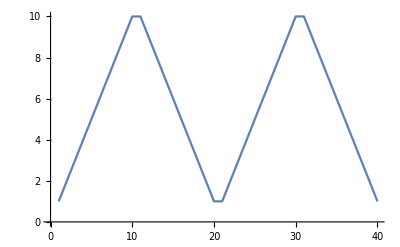
| Expected output: |  
  | -Graphics- |

Encuentre una forma más simple de {Range[10]+1,Range[10]-1,Reverse[Range[10]]}. »

| Expected output: |  
  | {{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}} |

Encuentre una forma más simple de Module[{u=10},Join[{u},Table[u=Mod[17u+2,11],20]]]. »

| Expected output: |  
  | {10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10} |

Genere 10 cadenas de caracteres aleatorios que consten de 5 letras, donde las consonantes estén alternadas con las vocales (aeiou). »

| Sample expected output: |  
  | {"nafam","toqay","xuheq","hawop","wiyoj","vozop","sasek","dabaw","xicap","yayok"} |

Preguntas y respuestas

Habiendo llegado a la Sección 38, ¿cómo es que apenas hasta ahora se introducen las asignaciones de variables?

Porque, como se ha visto, en Wolfram Language se puede llegar muy lejos sin necesidad de introducirlas. Además, un programa sin asignaciones resulta mucho más limpio.

Puede asignarse un nombre a cualquier cosa?

Sí. Ya sean gráficas, arreglos, imágenes, funciones puras, lo que sea.

¿Cómo se dice, en voz alta, x=4?

“x igual a 4”, o, menos frecuentemente, “asignar x a 4”, o “dar a x el valor 4”.

¿Qué principios pueden ser buenos para los nombres globales?

Use nombres específicos y explícitos. No hay que preocuparse de que sean demasiado largos; se autocompletarán al escribirlos. Para nombres “informales”, iniciarlos con letras minúsculas. En el caso de nombres pensados cuidadosamente, podrían usarse iniciales mayúsculas, como en las funciones nativas.

% se refiere al resultado anterior. Y, ¿en el caso del penúltimo y los que están antes?

%% da el penúltimo, %%% da el antepenúltimo, etc. %n da el resultado en la línea n (esto es, el resultado con etiqueta Out[n]).

¿Puede asignarse a varias variables al mismo tiempo?

Sí. x=y=6 asigna a x y a y el 6. {x,y}={3,4} asigna x a 3 y y a 4. {x,y}={y,x} intercambia los valores de x y y.

¿Qué sucede si se escapa una variable de un Module sin que le haya sido asignado un valor?

¡Inténtelo! Verá que hay una nueva variable a la que se le ha dado un nombre único.

¿Y qué hay con otras instrucciones de la programación procedimental, tales como Do y For?

También existen en Wolfram Language. A veces puede ser útil utilizar Do, especialmente cuando hay efectos secundarios, tales como la asignación de variables o la exportación de datos. Casi siempre, For es una mala idea y puede sustituirse por código mucho más limpio usando funciones como Table.

Notas técnicas

El resultado de x=2+2 es simplemente 4, pero se está haciendo una asignación para x como un efecto secundario.

En la programación funcional pura y simple, el único efecto de un cómputo es dar el resultado. En cuanto se empieza a asignar valores hay, en efecto, un estado oculto establecido por dichas asignaciones.

x=. es una forma alternativa de Clear[x].

Module efectúa un ámbito léxico, es decir, efectivamente limita a un ámbito el alcance de los nombres de las variables. Block efectúa un ámbito dinámico, es decir, delimita el ámbito de los valores, pero no los nombres de las variables. Ambas cosas son útiles en diferentes circunstancias. De hecho,Table usa Block.

x++ es equivalente a x=x+1. x+=n es equivalente a x=x+n. AppendTo[x,n] es equivalente a x=Append[x,n] o x=Join[x,{n}].